```mathematica
ClearAll["Global`*"]
```

```mathematica
(*test case 1*)
```

```mathematica
(*test case 2*)
```

```mathematica
u[x_]:={Cos[2 π x^2/L],Cos[2 π x^2/L]}
```

```mathematica
gradu[x_]:={-(4 π x Sin[(2 π x^2)/L])/L,-(4 π x Sin[(2 π x^2)/L])/L}
```

```mathematica
L=1;
```

```mathematica
(*check for u[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/u.csv"][[2;;]];
(*the solution obtained from finite elements is not unique -> it is determined up to a constant-> substract it off so you can compare with the exact one*)
t0=t[[1,1]];
t=Table[{t[[i,4]],t[[i,1]]- t0+u[0][[1]]},{i,2,Length[t]}]
```

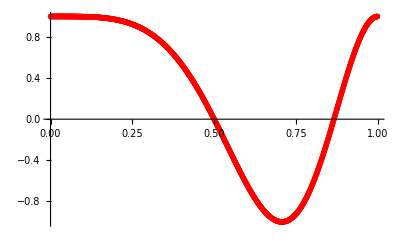

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

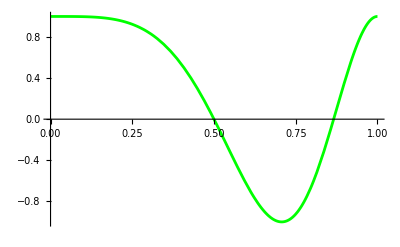

```mathematica
plotexact=Plot[u[x][[1]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]][[1]]],{i,1,Length[t]}]]
```

6.25×10^-7

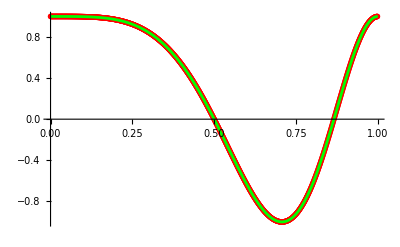

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*check for u[[2]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/u.csv"][[2;;]];
(*the solution obtained from finite elements is not unique -> it is determined up to a constant-> substract it off so you can compare with the exact one*)
t0=t[[1,2]];
t=Table[{t[[i,4]],t[[i,2]]- t0+u[0][[2]]},{i,2,Length[t]}]
```

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics-

```mathematica
plotexact=Plot[u[x][[2]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

-Graphics-

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]][[2]]],{i,1,Length[t]}]]
```

6.25×10^-7

```mathematica
Show[plotnum,plotexact]
```

-Graphics-